# Coherent states

The number states |n⟩ have a uniform phase distribution from 0 to 2π, meaning there is not a defined phase. One may think that the classical limit is when the number of photons of a number state goes to ∞ , but that is not the case because ⟨n| E_x|n⟩  = 0 for any n. We seek states such the expectation of the field operator oscillates sinusoidally , we introduce the coherent states  that are the “most classical” states of the quantum harmonic oscillator exploring its properties. Then we move on to an important topic in quantum optics, characteristic functions and phase space representations and its use in the QuantumFramework.

### Key Concepts

Coherent states

Displacement operator

Characteristic functions

Phase space representations

## Eigenstates of the annihilation operator and minimum uncertainty

If we consider the superposition of number states that differ in ± 1, for example |ψ⟩ = c_n|n⟩ + c_(n+1)|n+1⟩ will have non zero expectation for the electric field operator. More generally, a superposition of all number states will also hold that property, the replacement of â and (â)^† by continuous variables  produces a classical field. A unique way to perform the replacement is to find eigenstates of annihilation operator , in other words solving the eigenvalue equation 
 where α can be in general complex because the operator is not Hermitian.

We can expand |α⟩ in the complete Fock basis 

And replacing in the eigenstate equation and comparing coefficients we can get a recurrence relation C_n √n = α C_(n-1) which is not difficult to solve and  a compact form can be expressed in function of C_0
      C_0 can be found from normalization yielding

Using this we can define a not normalized coherent state in a truncated Fock space, the normalization can be done when needed

```mathematica
SetFockSpaceSize[30];
a := AnnihilationOperator[];
```

Not normalized symbolic coherent state:

```mathematica
αket = CoherentState[]
```

QuantumState[…]

Normalized coherent state:

```mathematica
coherent := CoherentState[]["Normalize"]
```

Right annihilation operator eigenstate(we compare the amplitudes except the last one because we are using a finite basis):

```mathematica
(a@αket- α αket)["Amplitudes"]//Values //Most
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Analyzing the expected value of the electric field operator:

```mathematica
Ex := ⅈ √((h ω)/(2 Subscript[ϵ, 0] V))(a Exp[ⅈ(Dot[k,r]-ω t)]-SuperDagger[a] Exp[-ⅈ(Dot[k,r]-ω t)]);
```

```mathematica
αrandom = 2 Exp[ⅈ Exp[RandomReal[{0,2π}]]];
```

```mathematica
meanEfield =With[{state=coherent[αrandom]},(SuperDagger[state]@Ex@state)["Scalar"]];
```

It is the same as  resembling a classical field:

```mathematica
classicalEfield =ⅈ √((h ω)/(2 Subscript[ϵ, 0] V)) (α Exp[ⅈ (k.r-ω t)]-Conjugate[α] Exp[-ⅈ (k.r-ω t)]);
```

```mathematica
Chop[meanEfield - (classicalEfield/.α->αrandom)//Simplify]
```

0.+0. ⅈ

Or in polar form,

```mathematica
FullSimplify[classicalEfield/. α->Abs[α] ⅇ^(ⅈ θ) ,Element[{t,ω,k,θ},Reals]]
```

-√2 Abs[α] Sin[θ-t ω+k.r] √((h ω)/(V ϵ_0))

It can be shown that  so    is one of the expressions that corresponds to the vacuum fluctuations so the coherent state has field mean classical-like values and mean fluctuations of the vacuum

```mathematica
meanEfieldSquared = With[{state=coherent[αrandom]},(SuperDagger[state]@(Ex@Ex)@state)["Scalar"]];
```

```mathematica
√Chop[FullSimplify[meanEfieldSquared-meanEfield^2]]
```

0.707107 √((h ω)/(V ϵ_0))

Another check is using the quadrature operators  X_i  from section 1.3 , the coherent states  minimize the uncertainty inequality with both quadrature uncertainties being the same.

```mathematica
{X1,X2} = QuadratureOperators[];
```

```mathematica
With[{s =αket[αrandom]["Normalize"]},OperatorVariance[s,#]&/@{X1,X2}]//Chop
```

{0.25,0.25}

The interpretation of α in a phase space context is α = ⟨ X_1⟩ + ⅈ ⟨ X_2⟩ obtained from seeking states that saturate the uncertainty inequality and solving certain eigenvalue equation given that [X_1,X_2] = ⅈ/2
Another physical interpretation of α is related to the photon number operator, it is easy to verify

The random α was chosen a complex number with norm 2, so the expectation returns 4

```mathematica
numberOp := SuperDagger[a]@a;
(SuperDagger[coherent[αrandom]]@numberOp@coherent[αrandom])["Scalar"]//Chop
```

4.

```mathematica
√OperatorVariance[coherent[αrandom],numberOp]//Chop
```

2.

This shows that the photon distribution follows a Poisson distribution, this is more clearly shown when calculating P_n the probability of measuring n photons. From the definition of coherent state in Fock basis it is not difficult to obtain 

The fractional uncertainty  decreases with increasing mean photon number. The phase distribution for a coherent state |α⟩ (α = |α| ⅇ^(ⅈ θ)) is 
  
For large |α| the Poisson distribution approximates to a Gaussian so a compact approximation can be derived

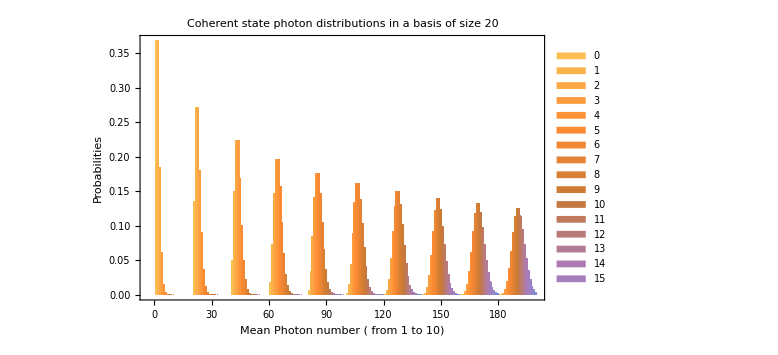

```mathematica
SetFockSpaceSize[20];
BarChart[Table[coherent[√x]["Probabilities"]//Values,{x,1.,10}],]
```

NOTE: Since we are using a truncated basis it is worth noting that to appropriately describe a coherent state with amplitude α, the basis size should be around 
|α |^2+5 |α| (or higher) to include the tails of the  Poisson distribution

For this example |α| = √10the best size would be 10+5 √10 ≈ 25

```mathematica
SetFockSpaceSize[25];
```

We can observe the corresponding photon number distribution:

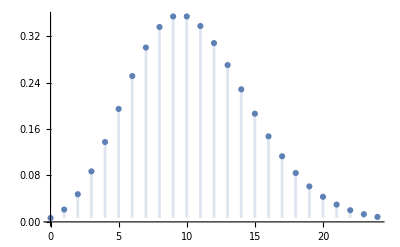

```mathematica
DiscretePlot[Sqrt @ PDF[PoissonDistribution[10],x],{x,0,24},Filling->Bottom]
```

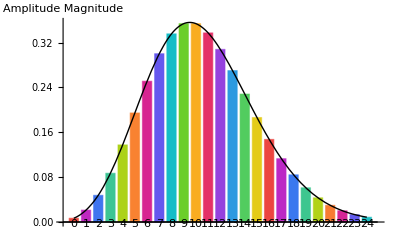

```mathematica
Show[coherent[√10 Exp[ⅈ RandomReal[{0,2π}]]]["AmplitudePlot",LabelStyle->8,ChartLegends->Automatic],Plot[Interpolation[Table[{x+1,Sqrt @ PDF[PoissonDistribution[10],x]},{x,0,24}]][y],{y,1,25},PlotStyle->{Black,Thick}],AxesLabel->{"","Amplitude Magnitude"},LabelStyle->10]
```

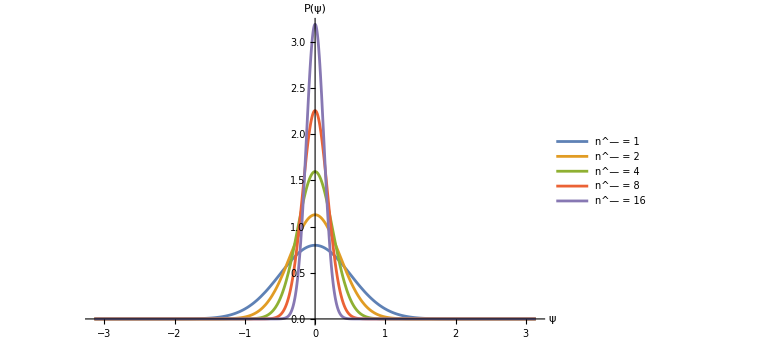

```mathematica
Plot[Evaluate[Table[√((2 Abs[x]^2)/π) Exp[-2 Abs[x]^2 (ψ-Arg[x])^2],{x,{√1,√2,√4,√8,√16}}]],{ψ,-π,π},]
```

So coherent states are quantum states with classical-like  features because:

Mean value of electric field has the form of a classical expression

Electric field fluctuations are those of the vacuum

Fluctuations in the photon number decrease when the mean photon number increases

Their phase becomes more localized when the mean photon number increases

## Displacement operator and displaced vacuum states

There exists an additional equivalent definition of a coherent state that is based on displacing the vacuum state , that can give more insight why coherent states have must have the uncertainty of the vacuum. The generator is the displacement operator that also has some nice algebraic properties, it is defined as:

and a coherent state can be build as

Using the disentangling theorem   valid when  but holds 
 so applying to vacuum 
Expanding    because the annihilation operator and their powers kill the vacuum state except when k = 0 , because   so D(α) |0⟩ is exactly the same as the previous definition

Verifying symbolically the displacement operator main property:

```mathematica
DisplacementOperator[α][]==CoherentState[][α]
```

True

Using a truncated basis has additional numeric error propagation because [a, a^†] is not exactly the identity. Using a bigger space size or reducing the magnitude of α can control the desired precision.

```mathematica
αrandom = RandomComplex[{2+2ⅈ,3+3ⅈ}];
```

```mathematica
SetFockSpaceSize[15];
```

```mathematica
(DisplacementOperator[αrandom][]-coherent[αrandom])["Amplitudes"]//Values
```

{-0.000338187,-0.000697612-0.000887893 ⅈ,0.000630802-0.0025902 ⅈ,0.00467749-0.00212864 ⅈ,0.00761869+0.00394478 ⅈ,0.00239661+0.0125845 ⅈ,-0.0114703+0.0131666 ⅈ,-0.0220085-0.00111671 ⅈ,-0.0150145-0.0212436 ⅈ,0.00826738-0.027747 ⅈ,0.0284296-0.0112358 ⅈ,0.0265763+0.0155168 ⅈ,0.00406546+0.0293822 ⅈ,-0.0190693+0.0197704 ⅈ,-0.0243855-0.00248102 ⅈ}

```mathematica
SetFockSpaceSize[45];
(DisplacementOperator[αrandom][]-coherent[αrandom])["Amplitudes"]//Values
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
DisplacementOperator[α]["Dagger"] == DisplacementOperator[-α]
```

True

It is clear  , is a unitary operator

Composing two displacement operators also has the form of a displacement operator times an overall phase factor 
 (can be proved with disentangling theorem)
 Intuitively if we do a displacement of α and then a displacement of β, the net displacement is α + β

```mathematica
SeedRandom[100];
{αrandom,βrandom}= RandomComplex[{-2-2I,2+2I},2]
```

{-1.94852-1.10714 ⅈ,-0.64538+0.777815 ⅈ}

We consider a bigger size because are composing displacements:

```mathematica
SetFockSpaceSize[50];
```

“AmplitudeList” returns non zero amplitudes, in this case all are zero so the states are the numerically the same

```mathematica
((DisplacementOperator[αrandom]@DisplacementOperator[βrandom][])-Exp[ⅈ Im[αrandom βrandom*]]coherent[αrandom + βrandom]//Chop)["AmplitudeList"]
```

{}

## Wave packets and time evolution

The position operator q̂ is defined, such that q̂ |q⟩ = q |q⟩ describes the position eigenstates:

```mathematica
SetFockSpaceSize[20];
```

```mathematica
q = √(h/(m ω)) QuadratureOperators[][[1]];
```

The Fock states wave functions are the following (derivations can be found in standard quantum mechanics textbooks regarding a quantum harmonic oscillator):
  where ξ = q √(m ω/h)  and H_n are Hermite polynomials

Then the wave function for a coherent state is:

It can be simplified and it takes the form of a gaussian, and the probability distribution |ψ_α(q)|^2 also takes the form of a gaussian

```mathematica
waveFuncCoh =((m ω)/(π h))^(1/4)ⅇ^(-Abs[α]^2/2)ⅇ^(-ξ^2/2)ⅇ^(ξ^2)FullSimplify[(ⅇ^(-ξ^2) Sum[(z)^n/n!HermiteH[n,ξ],{n,0,∞}])]/.z->α/√2
```

(ⅇ^(-(α/(√2)-ξ)^2+ξ^2/2-Abs[α]^2/2) ((m ω)/h)^(1/4))/π^(1/4)

Plot when α = 1

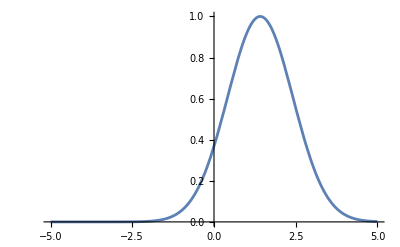

```mathematica
Plot[waveFuncCoh[[1]] /. α->1,{ξ,-5,5}]
```

The diagonal quantum harmonic oscillator Hamiltonian for a single mode field:

```mathematica
H = h ω (SuperDagger[a]@a +1/2 );
```

```mathematica
H["Formula"]
```

(h ω)/2 00+(3 h ω)/2 11+(5 h ω)/2 22+(7 h ω)/2 33+(9 h ω)/2 44+(11 h ω)/2 55+(13 h ω)/2 66+(15 h ω)/2 77+(17 h ω)/2 88+(19 h ω)/2 99+(21 h ω)/2 1010+(23 h ω)/2 1111+(25 h ω)/2 1212+(27 h ω)/2 1313+(29 h ω)/2 1414+(31 h ω)/2 1515+(33 h ω)/2 1616+(35 h ω)/2 1717+(37 h ω)/2 1818+(39 h ω)/2 1919

We create an evolution operator to evolve the states at any time:

```mathematica
QOE=QuantumOperator[QuantumEvolve[H/h,None,t],"Parameters"->t];
```

A coherent state  remains a coherent state under the evolution but the complex amplitude phase depends on time, with an extra global phase

```mathematica
(QOE @ CoherentState[]) == ⅇ^(-ⅈ ω t/2)CoherentState[][α ⅇ^(-ⅈ ω t)]
```

True

The mean value of the position operator for the evolved state, behaves like it was a classical oscillator (sinusoidal oscillations). This emphasises why coherent states are called “the most classical” quantum states. This also holds for the mean value of the momentum operator.

```mathematica
αc = RandomComplex[√2{-1-ⅈ,1+ⅈ}];
```

```mathematica
states=Table[{t,QOE[t][coherent[αc]]},{t,0,10,0.25}];
```

```mathematica
meanPosition=MapAt[((SuperDagger[#]@q@#)["Scalar"]&),#,2]& /@ states ;
```

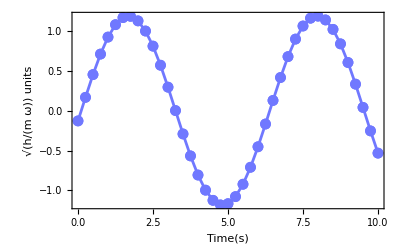

```mathematica
ListLinePlot[Re[meanPosition/.{h->1,m->1,ω->1}],]
```

## More properties of coherent states

The  inner  product   of  two  coherent  states | α⟩,  | β ⟩ is 

So when α and β are different clearly the states are not orthogonal , but when the quantity |β - α|^2 is large the states are almost orthogonal ( ⟨ β | α⟩ ≈ 0)

```mathematica
{αc,βc} = RandomComplex[{1.5+1.5I},2];
```

```mathematica
(coherent[αc]["Dagger"]@coherent[βc])["Scalar"]
```

0.304094-0.00792897 ⅈ

```mathematica
Exp[-1/2(βc*αc-βc αc*)]Exp[-1/2 Abs[βc-αc]^2]
```

0.304094-0.00792897 ⅈ

The coherent states have a completeness relation  over the complex α plane given by

We include the exact normalization constant in the case of an infinite basis so we can try to reproduce the theoretical results(here 5 refers to the Fock space size):

```mathematica
Exp[-Abs[α]^2](CoherentState[5]@SuperDagger[CoherentState[5]])["Matrix"]//MatrixForm
```

(ⅇ^(-Abs[α]^2) | ⅇ^(-Abs[α]^2) Conjugate[α] | (ⅇ^(-Abs[α]^2) Conjugate[α]^2)/(√2) | (ⅇ^(-Abs[α]^2) Conjugate[α]^3)/(√6) | (ⅇ^(-Abs[α]^2) Conjugate[α]^4)/(2 √6)
α ⅇ^(-Abs[α]^2) | α ⅇ^(-Abs[α]^2) Conjugate[α] | (α ⅇ^(-Abs[α]^2) Conjugate[α]^2)/(√2) | (α ⅇ^(-Abs[α]^2) Conjugate[α]^3)/(√6) | (α ⅇ^(-Abs[α]^2) Conjugate[α]^4)/(2 √6)
(α^2 ⅇ^(-Abs[α]^2))/(√2) | (α^2 ⅇ^(-Abs[α]^2) Conjugate[α])/(√2) | 1/2 α^2 ⅇ^(-Abs[α]^2) Conjugate[α]^2 | (α^2 ⅇ^(-Abs[α]^2) Conjugate[α]^3)/(√12) | (α^2 ⅇ^(-Abs[α]^2) Conjugate[α]^4)/(2 √12)
(α^3 ⅇ^(-Abs[α]^2))/(√6) | (α^3 ⅇ^(-Abs[α]^2) Conjugate[α])/(√6) | (α^3 ⅇ^(-Abs[α]^2) Conjugate[α]^2)/(√12) | 1/6 α^3 ⅇ^(-Abs[α]^2) Conjugate[α]^3 | 1/12 α^3 ⅇ^(-Abs[α]^2) Conjugate[α]^4
(α^4 ⅇ^(-Abs[α]^2))/(2 √6) | (α^4 ⅇ^(-Abs[α]^2) Conjugate[α])/(2 √6) | (α^4 ⅇ^(-Abs[α]^2) Conjugate[α]^2)/(2 √12) | 1/12 α^4 ⅇ^(-Abs[α]^2) Conjugate[α]^3 | 1/24 α^4 ⅇ^(-Abs[α]^2) Conjugate[α]^4)

These integrals can be quite slow:

```mathematica
Integrate[1/24 α^4 ⅇ^(-Abs[α]^2) Conjugate[α]^4/.α->x+y ⅈ,{x,-∞,∞},{y,-∞,∞}]//AbsoluteTiming
```

{58.3925,π}

```mathematica
Integrate[(α^3 ⅇ^(-Abs[α]^2) Conjugate[α]^2)/(√12)/.α->x+y ⅈ,{x,-∞,∞},{y,-∞,∞}]//AbsoluteTiming
```

{23.8902,0}

The m,n  matrix element of the result is    switching to polar coordinates α = r e^(ⅈ θ), ⅆ^2 α = r ⅆr ⅆθ

We evaluate the integral for general m and n, showing the completeness relation:

```mathematica
Table[{assump,
FullSimplify[
Integrate[Sqrt[1/(m! n!)] r^(m+n+1) Exp[-r^2] Exp[I (m-n) θ],{r,0,∞},{θ,0,2 π},Assumptions->assump],Element[{m,n},Integers]&&n>=0&&m>=0]},
{assump,{m==n,m != n}}] //
TableForm[#,TableHeadings->{None,{"Case", "Result"}}]&
```

Case | Result
m==n | π
m≠n | 0

```mathematica
Integrate[Normal[r( Exp[-Abs[α]^2](CoherentState[10]@SuperDagger[CoherentState[10]]))["Matrix"]]/. α->r ⅇ^(ⅈ θ),{r,0,∞},{θ,0,2π}]//MatrixForm
```

(π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π)

Any state can be decomposed in terms of coherent states:

When the state is also a coherent state | β ⟩, we see the coherent states are not linear independent and are said to be “overcomplete”, the inner product of the coherent states (exponential factor)  is called a reproducing kernel

## Characteristic functions and quasi-probability distributions

If we have a probability density p(x) associated with a random variable X, it should be the case that p(x) >= 0   ∀ x ∈ ℝ and ∫ p(x) ⅆx=1 . The nth moment of the probability density is   , provided information about all moments  the function p(x) is determined. Because we can define a characteristic function  so they are related by a Fourier transform

Three characteristic functions are important in quantum optics:



related by  C_W(λ) = C_N(λ)ⅇ^(-1/2 |λ|^2)=C_A(λ)ⅇ^(1/2 |λ|^2)
There is also a general parametrized characteristic function 
  with C(λ,0) = C_W(λ), C(λ,1) = C_N(λ) and C(λ, -1) = C_A(λ)
The characteristic functions are related to quasi-probability distributions , the Wigner function is the Fourier transform of the Weyl-ordered characteristic function

The Husimi Q-function can be obtained from the Fourier transform of the anti-normally ordered characteristic function

Finally the  Glauber-Sudarshan P-function is the Fourier transform of the normally orderer characteristic function

These functions can be difficult to calculate for an arbitrary state or density matrix , there exist good numerical techniques to compute the Wigner and Husimi Q-function , but for the Glauber P-function is difficult  to develop stable numerical algorithms because it has singularities. The Husimi function is always positive, unlike the Wigner and P-function that can take negative values in some region that  indicate nonclassical behavior, however the converse is not a true a state can be nonclassical and still have positive Wigner function. The P-function is a good theoretical tool but impractical in terms of numerical algorithms because there are cases it can get even more singular than a Delta-function, this is why the preferred of all three is the Wigner because it can also show quantum nature of nonclassical states (unlike Husimi).

Husimi Q-function plots:

For Fock state  and coherent state  :

```mathematica
SetFockSpaceSize[20];
```

```mathematica
Block[{husi = HusimiQRepresentation[#,{-5,5},{-5,5}]},Plot3D[husi[x,p], {x,-5,5},{p,-5,5},
ColorFunction->"Rainbow",
PlotLegends->Automatic,
PlotPoints->100,
AxesLabel->{"Re(α)","Im(α)","Q(α)"},
PlotRange->All,
ImageSize->400,
LabelStyle->15]] & /@ {FockState[3],coherent[1+ⅈ]}//Column
```

-Graphics3D-
-Graphics3D-

Wigner plots:

```mathematica
Block[{wig = WignerRepresentation[#,{-5,5},{-5,5}]},Plot3D[wig[x,p], {x,-5,5},{p,-5,5},
ColorFunction->"Rainbow",
PlotLegends->Automatic,
PlotPoints->100,
AxesLabel->{"Re(α)","Im(α)","W(α)"},
PlotRange->All,
ImageSize->400,
LabelStyle->15]] & /@ {FockState[3],coherent[1+ⅈ]}//Column
```

-Graphics3D-
-Graphics3D-

Getting Husimi Q function from Wigner(gaussian filtering):

```mathematica
wig = WignerRepresentation[FockState[2],{-4,4},{-4,4}];
```

```mathematica
husi = HusimiQRepresentation[FockState[2],{-4,4},{-4,4}];
```

Numerical integration:

```mathematica
Q[xα_,pα_]:= 2/π NIntegrate[wig[x,p] ⅇ^(-(x-xα)^2)ⅇ^(-(p-pα)^2),{x,-4,4},{p,-4,4},Method->"LocalAdaptive"]
```

Difference compared to HusimiQRepresentation

```mathematica
diff =Abs[husi[#1,#2]-Q[#1,#2]]& @@@RandomReal[{-4,4},{50,2}];
```

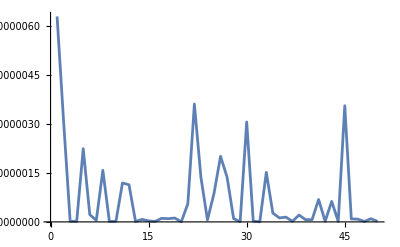

```mathematica
ListLinePlot[diff,PlotRange->All]
```

s-parametrized Wigner function:

```mathematica
sParameterWigner[func_,s_,xα_,pα_]:= 4/(π(1-s))NIntegrate[func[x,p] ⅇ^(-2/(1-s)((x-xα)^2+(p-pα)^2)),{x,-4,4},{p,-4,4},Method->"LocalAdaptive",MaxRecursion->2,AccuracyGoal->4]
```

Visualization varying the s parameters , we do not go up to 1 because in that limit it becomes the Glauber ( can take a while):

```mathematica
ListAnimate[Table[DensityPlot[sParameterWigner[wig,s,x,p],{x,-4,4},{p,-4,4},PlotRange->All,PlotPoints->40,ColorFunction->"Rainbow",FrameLabel->{"x","p","W_s(x,p)"},LabelStyle->13,PlotLabel->"Wigner generalized s-parameter function for |2⟩",PlotLegends->Automatic],{s,-1,0.9,0.1}],DefaultDuration->15]
```

## Paclet installation

Install  the Quantum Framework paclet:

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

Load quantum framework functions:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load quantum framework functions for the second quantization:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```